```mathematica
ClearAll["Global`*"]
```

# A multigait microrobot driven by powerful, high - frequency combustion actuators

Cameron A. Aubin^1,  Ronald H.Heisser^1, Ofek Peretz^2, Julia Timko^1, Jacqueline Lo^1, E. Farrell Helbling^3,  Sadaf Sobhani^1, Amir D.Gat^2, Robert F.Shepherd^(*1)

^1Sibley School of Mechanical and Aerospace Engineering, Cornell University; Ithaca, New York 14853, USA.
^2Faculty of Mechanical Engineering, Technion-Israel Institute of Technology; Haifa 3200003, Israel.
^3Department of Electrical and Computer Engineering, Cornell University; Ithaca, New York 14853, USA.

*Corresponding author. Email: rfs247@cornell.edu

## Auxiliary Functions

```mathematica
clean2[expr_] := 
 HoldForm[expr] /. 
  h_Symbol[args___] /; Context@Unevaluated@h =!= "System`" :> h
```

```mathematica
pdConv[f_] := 
 TraditionalForm[  f /. Derivative[inds__][g_][vars__] :>     Apply[Defer[D[g[vars], ##]] &, 
     Transpose[{{vars}, {inds}}] /. {{var_, 0} :> 
        Sequence[], {var_, 1} :> {var}}]]
```

```mathematica
TextbookEqOLD[expr_] := TableForm[TraditionalForm[{expr  // pdConv }[[1]][[1]] // clean2]]
```

```mathematica
centering:=CellPrint[ExpressionCell[#,"Output",TextAlignment->Center]]&
```

```mathematica
TextbookEq[expr_] := TraditionalForm[{TableForm[expr]  // pdConv }[[1]][[1]] // clean2]//centering
```

```mathematica
TextbookEqListNames[expr_] := TraditionalForm[{TableForm[expr,TableDirections->Row]  // pdConv }[[1]][[1]] // clean2]//centering
```

```mathematica
$PrePrint=Style[#,"Output",TextAlignment->Center]&;
```

## Overview

Nomenclature:
d_in       - Inlet diameter                                        d_out     - Outlet diameter
q_in       - Inlet volumetric flux                            q_out      - Outlet volumetric flux
T_in       - Chamber temperature                       T_atm    - Ambient temperature
p_in       - Chamber pressure                               p_atm    - Ambient pressure
V_in       - Chamber volume                                  H_T       - heat transfer coefficient
m_rob   - Robot’s main body mass                   m_leg    - Robot’s leg mass
d_mem  - Membrane diameter                            t_m        - Membrane thickness
E_m          - Membrane Young’s modulus        ρ          - Membrane Density
ν_m          - Membrane Poisson’s ratio             μ          - Gas viscosity

-Graphics-

## Listing the governing equations

```mathematica
ListOfAssumptions = {p[t] > 0, t > 0, R > 0, ρ[t] > 0, k > 0, V0 > 0, V > 0, Reals};
```

### Flow equations

Perfect Gas equation

```mathematica
PerfectGasEq=p[t]==ρ[t] R[t] T[t];TextbookEq[PerfectGasEq]
```

p==R T ρ

Mass conservation equation

```mathematica
MassConservationEq=qOut[t]==qInC-D[ρ[t]V[t],t];TextbookEq[MassConservationEq]
```

qOut==qInC-(∂ρ)/(∂t) V-(∂V)/(∂t) ρ

Hagen Poiseuille equation for gas exiting the chamber

```mathematica
qOutEq=qOut[t]== ρ[t] (π rEx^4)/(8 μ)(p[t]-pAtm)/lExit;TextbookEq[qOutEq]
```

qOut==(π rEx^4 (-pAtm+p) ρ)/(8 lExit μ)

This equation is for an incompressible fluid. For a compressible fluid there is a different equation. The difference is significant only if the pressure within the chamber is O(Atm).

### Elasticity

Elastic relation between chamber volume and pressure

```mathematica
ElasticReBen=w/rc==1/5(12(1-pr^2)q/ ( 64 Em h^3))(rc^2-r^2)^2;
wFunc[r_,q_,rc_,h_,Em_,pr_]=Flatten[Solve[ElasticReBen,w]][[1]][[2]];
VtoPEq=V[t]-V0==Integrate[wFunc[r,p[t]-pAtm,rc,h,Em,pr] 2 π r,{r,0,rc}];TextbookEq[VtoPEq]
```

-V0+V==(π (-1+pr^2) rc^7 (pAtm-p))/(80 Em h^3)

### Species concentrations

The number of molecules within a chamber does not change during combustion, so the specific gas constant can be calculated by.

```mathematica
GasConstantEq=R[t]==(1000(mO2[t]/32+mCH4[t]/160+mCO2[t]/44+mH2O[t]/18+mN2[t]/24)/(mN2[t]+mO2[t]+mCH4[t]+mCO2[t]+mH2O[t]) )8.314;
DensityEq=ρ[t] V[t] ==mO2[t]+mN2[t]+mCH4[t]+mCO2[t]+mH2O[t];
mCH4ConservationEq=D[mCH4[t],t]==mCH4In-HeavisideTheta[qOut[t]]qOut[t] (mCH4[t]/(V[t] ρ[t]))-16 α IsIgnitionFunc[t,fr,dt] HeavisideTheta[mCH4[t]];
mO2ConservationEq=D[mO2[t],t]==mO2In-HeavisideTheta[mO2[t]]HeavisideTheta[qOut[t]]qOut[t] (mO2[t]/(V[t] ρ[t]))-HeavisideTheta[-qOut[t]]qOut[t] 0.21-64α IsIgnitionFunc[t,fr,dt] HeavisideTheta[mCH4[t]];
mCO2ConservationEq=D[mCO2[t],t]==-HeavisideTheta[qOut[t]]qOut[t] (mCO2[t]/(V[t] ρ[t]))+44 α IsIgnitionFunc[t,fr,dt] HeavisideTheta[mCH4[t]];
mH20ConservationEq=D[mH2O[t],t]==-HeavisideTheta[qOut[t]]qOut[t] (mH2O[t]/(V[t] ρ[t]))+H2OK 36 α IsIgnitionFunc[t,fr,dt] HeavisideTheta[mCH4[t]];
mN2ConservationEq=D[mN2[t],t]==-HeavisideTheta[qOut[t]]qOut[t] (mN2[t]/(V[t] ρ[t]))-HeavisideTheta[-qOut[t]]qOut[t] 0.79;
```

Upon combustion, one moll of CH4 vanishes, and along with 2 molls of O2. Two molls of H20 are created as well as 1 moll of CO2. 
 CH4+2O2->CO2+2H2O.

### Ignition and energy equations

First we model the time in which ignition occurs

```mathematica
HeatEquation = D[ρ[t] V[t] Cp T[t], t] == -hT π rc rc (T[t] - Tatm) + 16 HeatGen α IsIgnitionFunc[t, fr, dt] HeavisideTheta[mCH4[t]] + (qInC TAtm - qOut[t] T[t]) Cp - p[t] D[V[t], t];
TextbookEq[HeatEquation]
```

Cp (∂ρ)/(∂t) T V+Cp (∂V)/(∂t) T ρ+Cp (∂T)/(∂t) V ρ==16 HeatGen α mCH4 IsIgnitionFunc-(∂V)/(∂t) p-hT π rc^2 (-Tatm+T)+Cp (qInC TAtm-qOut T)

## Analysis

Lets define a list with all of our equations

```mathematica
EquationList={PerfectGasEq,MassConservationEq,qOutEq,VtoPEq,GasConstantEq,DensityEq,mCH4ConservationEq,mO2ConservationEq,mCO2ConservationEq,mH20ConservationEq,mN2ConservationEq,HeatEquation};
TextbookEq[EquationList]
```

p==R T ρ
qOut==qInC-(∂ρ)/(∂t) V-(∂V)/(∂t) ρ
qOut==(π rEx^4 (-pAtm+p) ρ)/(8 lExit μ)
-V0+V==(π (-1+pr^2) rc^7 (pAtm-p))/(80 Em h^3)
R==(8314. (mCH4/160+mCO2/44+mH2O/18+mN2/24+mO2/32))/(mCH4+mCO2+mH2O+mN2+mO2)
V ρ==mCH4+mCO2+mH2O+mN2+mO2
(∂mCH4)/(∂t)==mCH4In-16 α mCH4 IsIgnitionFunc-(qOut mCH4 qOut)/(V ρ)
(∂mO2)/(∂t)==mO2In-64 α mCH4 IsIgnitionFunc-0.21 -qOut qOut-(mO2 qOut mO2 qOut)/(V ρ)
(∂mCO2)/(∂t)==44 α mCH4 IsIgnitionFunc-(qOut mCO2 qOut)/(V ρ)
(∂mH2O)/(∂t)==36 H2OK α mCH4 IsIgnitionFunc-(qOut mH2O qOut)/(V ρ)
(∂mN2)/(∂t)==-0.79 -qOut qOut-(qOut mN2 qOut)/(V ρ)
Cp (∂ρ)/(∂t) T V+Cp (∂V)/(∂t) T ρ+Cp (∂T)/(∂t) V ρ==16 HeatGen α mCH4 IsIgnitionFunc-(∂V)/(∂t) p-hT π rc^2 (-Tatm+T)+Cp (qInC TAtm-qOut T)

```mathematica
NameList = {"PerfectGasEq", "MassConservationEq", "qOutEq", "VtoPEq", "GasConstantEq", "DensityEq", "mCH4ConservationEq", "mO2ConservationEq", "mCO2ConservationEq", "mH20ConservationEq", "mN2ConservationEq", "HeatEquation"};
```

```mathematica
qOutFunc[t_]=Flatten[Solve[EquationList[[3]],qOut[t]]][[1]][[2]];
EquationList1=Simplify[EquationList//.qOut->Function[t,qOutFunc[t]]];
ρFunc[t_]=Flatten[Solve[EquationList1[[6]],ρ[t]]][[1]][[2]];
EquationList2=Simplify[EquationList1//.ρ->Function[t,ρFunc[t]]];
VFunc[t_]=Flatten[Solve[EquationList2[[4]],V[t]]][[1]][[2]];
EquationList3=Simplify[EquationList2//.V->Function[t,VFunc[t]],ListOfAssumptions];
TFunc[t_]= Flatten[Solve[EquationList3[[1]],T[t]]][[1]][[2]];
EquationList4=Simplify[EquationList3//.T->Function[t,TFunc[t]],ListOfAssumptions];
RFunc[t_]=Solve[EquationList4[[5]],R[t]][[1]][[1]][[2]];
EquationList5=EquationList4//.R->Function[t,RFunc[t]];
```

```mathematica
QinO2=100;(*ml/min*)
ρO2=1.331;(*kg/m^3*)
ρNH4=0.668;(*kg/m^3*)
mInO2=QinO2/60 ρO2/10^6;
QinNH4val=18/60 ρNH4/10^6;
```

```mathematica
PRV={rEx->.2/1000,pAtm->101325.0,TAtm->300,V0->(π 0.003 0.003 0.0035),lExit->3.0/1000,hT->0.05*1000,Cp->0.5*1000,HeatGen->0.65*55 10^6,Tatm->300,μ->10^-5,pr->0.49,h-> 50 10^(-6),Em->0.7(10^5)*1000,ρs->1000,rc->0.003,
mO2In->mInO2,
mCH4In-> QinNH4val,
qInC->mInO2+QinNH4val,
 fr->10,dt->10^-4,MaxStepSizeVal->0.0151/100,α->5*5*10^-10,H2OK->1,NCycles->10,Tmax->0.02+3/10};
IsIgnitionFunc[t_,fr_,dt_]=Sum[PDF[NormalDistribution[i/fr+0.01,dt],t],{i,0,3,1}];
EquationList6=EquationList5//.PRV;
{mO20,mCO20,mH2O0,mCH40,mN20}={4.537 10^-8,0,0,0,0};
s=NDSolve[{EquationList6[[7]],EquationList6[[8]],EquationList6[[9]],EquationList6[[10]],EquationList6[[11]],EquationList6[[12]],p[0]==101372,mCH4[0]==mCH40,mO2[0]==mO20,mN2[0]==mN20,mCO2[0]==mCO20,mH2O[0]==mH2O0},{mCH4,mO2,mCO2,mH2O,mN2,p},{t,0,Tmax//.PRV},MaxStepSize->MaxStepSizeVal//.PRV,AccuracyGoal->20];
```

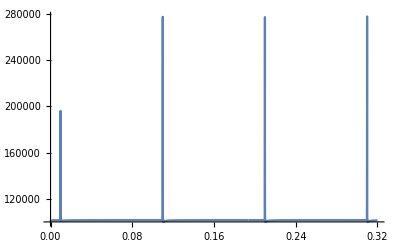

```mathematica
sol=First[p/.s];
Plot[sol[t],{t,0,Tmax/.PRV},PlotRange->All,PlotPoints->10000]
```

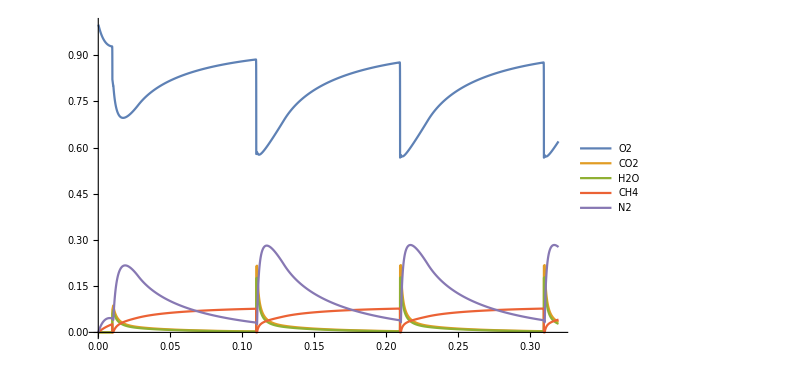
-Graphics-ConcentrationTime [sec]

```mathematica
m[t_] = (Evaluate[mO2[t] /. s] + Evaluate[mCO2[t] /. s] + Evaluate[mH2O[t] /. s] + Evaluate[mCH4[t] //. s] + Evaluate[mN2[t] //. s]);
PanelA = Labeled[Plot[{(mO2[t] /. s)/m[t], (mCO2[t] /. s)/m[t], (mH2O[t] /. s)/m[t], (mCH4[t] /. s)/m[t], (mN2[t] /. s)/m[t]}, {t, dt //. PRV, Tmax //. PRV}, PlotLegends -> {"O2", "CO2", "H2O", "CH4", "N2"}, PlotPoints -> 1800, PlotRange -> All, ImageSize -> 600], {Style[Text[Rotate["Concentration", 90 Degree]], 14], Style["Time [sec]", 14]}, {Left, Bottom}]
```